### Fit to a Sin with errors on the data

```mathematica
n=12;data=Table[Block[{x=i/n},{x,Sin[2π x]+RandomVariate[NormalDistribution[0,.25]]}],{i,n}];
```

#### To reproduce my plots: This was my random data:

```mathematica
data={{1/12,0.30009765776588543},{1/6,1.0099245369870868},{1/4,0.552041656275049},{1/3,0.6782906443728428},{5/12,0.23353424717635118},{1/2,-0.04633132222307028},{7/12,-0.711191469762885},{2/3,-0.8844005872021904},{3/4,-1.2023053107149948},{5/6,-0.533481852807481},{11/12,-1.1660639509295252},{1,0.09547461445128798}};
```

```mathematica
fitdata=data⟦{1,4,5,6,7,8,9,10,11,12}⟧;
```

#### Look at the "true" curve and the data points

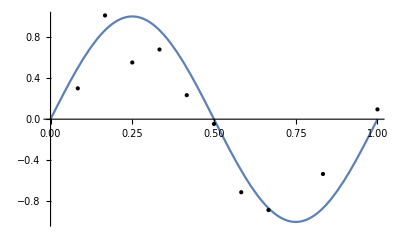

```mathematica
plot=Plot[Sin[2π x],{x,0,1},Epilog->{Point/@data}]
```

#### First, fit to all the points:

```mathematica
fits=Table[Normal[LinearModelFit[data,Table[x^i,{i,n}],x]],{n,9}];
```

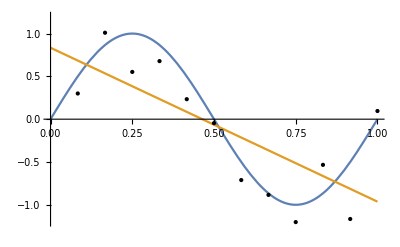
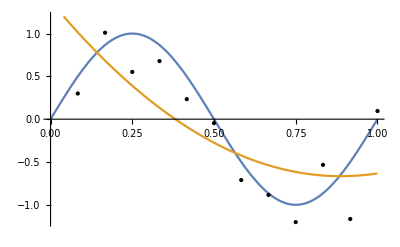
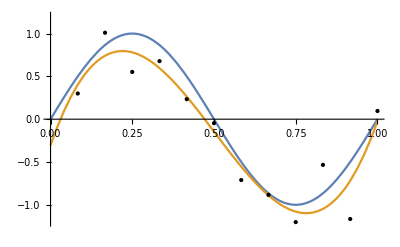
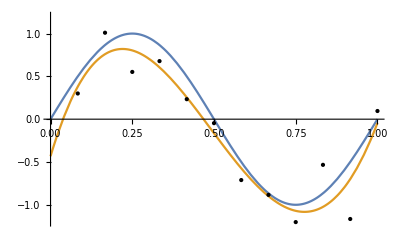
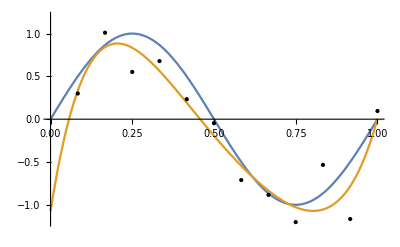
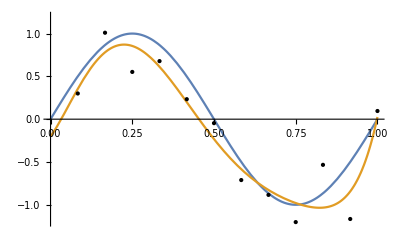
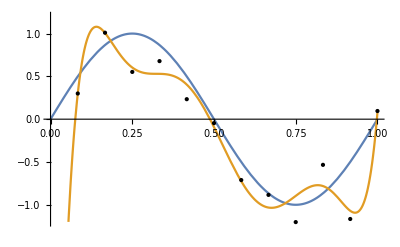
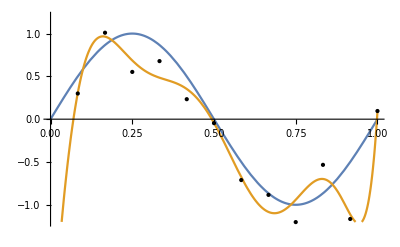

```mathematica
Plot[{Sin[2π x],#},{x,0,1},Epilog->{Point/@data},PlotRange->{-1.2,1.2}]&/@fits
```

```mathematica
errors[fits_,data_]:=Table[Total[(#⟦2⟧-fits⟦n⟧/.x->#⟦1⟧)^2&/@data],{n,9}]
```

```mathematica
errors[fits,data]
```

{2.87404,2.44045,0.669542,0.665694,0.6323,0.614879,0.242532,0.211086,0.0707446}

The errors are extremely small, but the curve is not really good... Overfitting!

#### Now, use only 10 of the points for fitting and the rest for testing:

```mathematica
m=10;fitdata=RandomSample[data,m];
```

```mathematica
fits2=Table[Normal[LinearModelFit[fitdata,Table[x^i,{i,n}],x]],{n,9}];
```

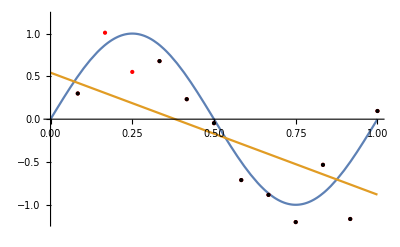
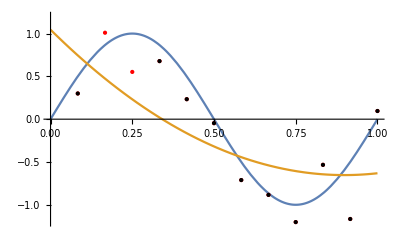
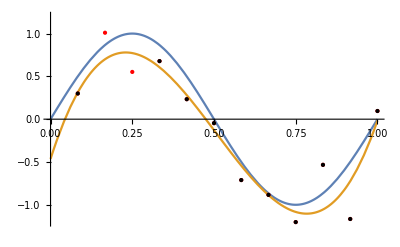
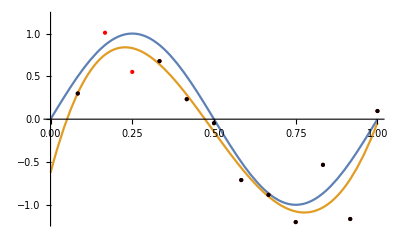
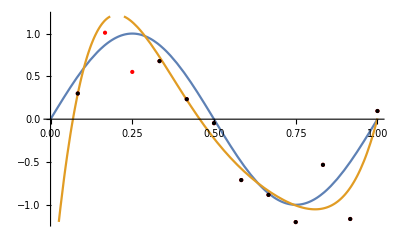
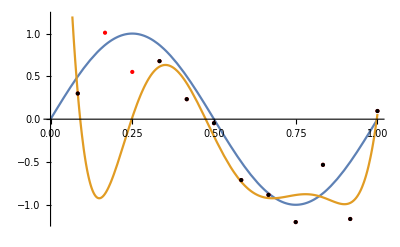
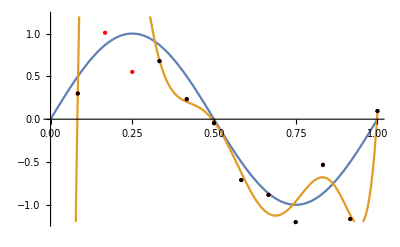
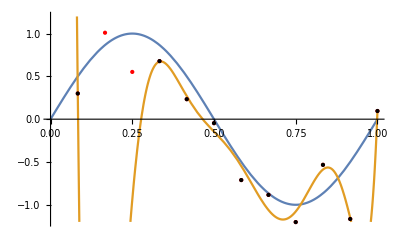

```mathematica
Plot[{Sin[2π x],#},{x,0,1},Epilog->{Red,Point/@data,Black,Point/@fitdata},PlotRange->{-1.2,1.2}]&/@fits2
```

```mathematica
errors[fits2,data]
```

{3.10758,2.60444,0.680316,0.674712,0.852531,4.16646,32.5715,52.4666,6001.62}

Higher order fits are good for the fit data but bad for the test data! We should use only 3rd or 4th (/5th) order!

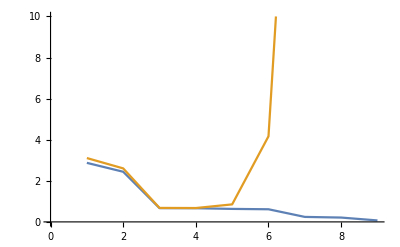

```mathematica
ListPlot[{errors[fits,data],errors[fits2,data]},Joined->True,PlotRange->{0,10}]
```

#### An alternative: Renormalisation, i.e. add a penalty for large coefficients

```mathematica
polynomial[k_]:=Sum[a[i] x^i,{i,0,k}];renorm[k_,λ_]:=λ Sum[a[i]^2,{i,k}];coeffs[k_]:=Table[{a[i],0,1},{i,0,k}];
```

NB: No renormalisation term for a_0 (c.f. Bishop), give starting values for coefficient search

```mathematica
fitstest=Table[FindMinimum[Total[(#⟦2⟧-polynomial[n]/.x->#⟦1⟧)^2&/@data],coeffs[n]],{n,9}];
```

```mathematica
%⟦3⟧
```

{0.669542,{a[0]→-0.306623,a[1]→11.044,a[2]→-32.1249,a[3]→21.3664}}

```mathematica
{errors[fits,data]⟦3⟧,fits⟦3⟧}
```

{0.669542,-0.306624+11.044 x-32.1249 x^2+21.3664 x^3}

Very nice, we agree with Mathematica's fit. Now let us include the penalty / renormalisation:

```mathematica
fitsrenorm[λ_]:=Table[polynomial[n]/.
FindMinimum[Total[(#⟦2⟧-polynomial[n]/.x->#⟦1⟧)^2&/@data]+renorm[n,λ],coeffs[n]]⟦2⟧,{n,9}];
```

How large should λ be?

```mathematica
fitsrenorm[0.1]
```

{0.745338-1.63361 x,0.739593-1.59759 x-0.0366009 x^2,0.824238-1.76694 x-0.726131 x^2+0.90817 x^3,0.874249-1.70019 x-1.15003 x^2+0.0939382 x^3+1.27956 x^4,0.887118-1.5444 x-1.32287 x^2-0.388751 x^3+0.559142 x^4+1.34996 x^5,0.880596-1.39074 x-1.3586 x^2-0.640823 x^3+0.122726 x^4+0.766717 x^5+1.2786 x^6,0.866964-1.26884 x-1.33376 x^2-0.756801 x^3-0.126634 x^4+0.403379 x^5+0.821189 x^6+1.14737 x^7,0.852507-1.18163 x-1.2885 x^2-0.798793 x^3-0.261252 x^4+0.184231 x^5+0.528796 x^6+0.792885 x^7+0.998371 x^8,0.839895-1.12294 x-1.24155 x^2-0.803527 x^3-0.328901 x^4+0.0556265 x^5+0.345871 x^6+0.560529 x^7+0.725055 x^8+0.853312 x^9}

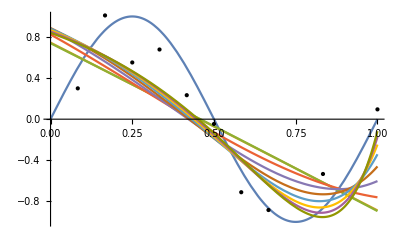

```mathematica
Plot[{Sin[2π x],%},{x,0,1},Epilog->{Point/@data}]
```

Much too large! We completely suppress the higher order polynomials.

```mathematica
fitsrenorm[10^-4]
```

{0.834346-1.79793 x,1.37845-4.59667 x+2.58371 x^2,-0.143317+9.58666 x-28.9804 x^2+19.4689 x^3,0.0254436+6.91073 x-17.689 x^2+2.46055 x^3+8.29425 x^4,0.0256892+6.90797 x-17.6835 x^2+2.46768 x^3+8.26969 x^4+0.0144988 x^5,0.0112989+6.97517 x-17.2702 x^2+0.996675 x^3+7.8853 x^4+3.83666 x^5-2.44383 x^6,0.0470258+6.4245 x-15.0851 x^2-1.12988 x^3+6.35823 x^4+3.61021 x^5+3.85648 x^6-4.09768 x^7,0.00555847+7.03607 x-17.3554 x^2+0.774147 x^3+7.96361 x^4+4.43636 x^5-1.31737 x^6-3.24699 x^7+1.69531 x^8,0.0633026+6.08064 x-12.6159 x^2-7.94738 x^3+11.2881 x^4+8.5988 x^5+0.719671 x^6-7.41365 x^7-3.70132 x^8+4.92707 x^9}

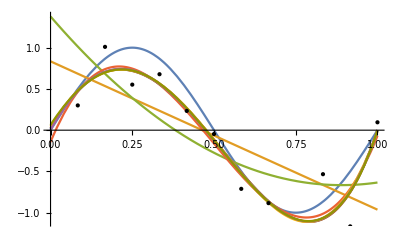

```mathematica
Plot[{Sin[2π x],%},{x,0,1},Epilog->{Point/@data}]
```

Great!!! But we need to be careful: At 10^-7we already see artefacts

```mathematica
fitsrenorm[10^-7]
```

{0.834444-1.79811 x,1.38117-4.60985 x+2.59545 x^2,-0.306442+11.0424 x-32.1214 x^2+21.3643 x^3,-0.430718+12.7381 x-38.5347 x^2+30.3148 x^3-4.13126 x^4,-0.969292+22.3715 x-91.6228 x^2+152.838 x^3-128.692 x^4+46.0719 x^5,-0.666514+15.5967 x-40.6463 x^2-20.948 x^3+165.281 x^4-194.302 x^5+75.698 x^6,-0.441692+10.9715 x-11.9804 x^2-82.8188 x^3+164.031 x^4-17.4903 x^5-146.704 x^6+84.4602 x^7,-0.358102+10.4299 x-21.9467 x^2+8.2508 x^3-84.1793 x^4+177.365 x^5+50.3097 x^6-298.273 x^7+158.445 x^8,-0.180566+8.09737 x-17.9585 x^2+31.6309 x^3-138.791 x^4+140.493 x^5+100.071 x^6+10.7396 x^7-345.78 x^8+211.736 x^9}

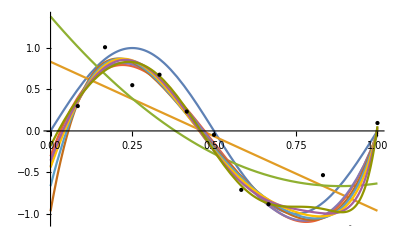

```mathematica
Plot[{Sin[2π x],%},{x,0,1},Epilog->{Point/@data}]
```

And at 10^-12, the effect of the renormalisation is not sufficient anymore to suppress the high order polynomials:

```mathematica
fitsrenorm[10^-12]
```

{0.834444-1.79811 x,1.38117-4.60986 x+2.59546 x^2,-0.306623+11.044 x-32.1249 x^2+21.3664 x^3,-0.432799+12.7654 x-38.6347 x^2+30.4509 x^3-4.19285 x^4,-1.07311+24.1811 x-101.347 x^2+174.807 x^3-150.635 x^4+54.071 x^5,-0.707641+15.9822 x-39.7989 x^2-33.9152 x^3+200.192 x^4-230.939 x^5+89.2046 x^6,-0.0157732+2.41599 x+42.8468 x^2-229.499 x^3+317.324 x^4-6.08767 x^5-270.669 x^6+143.722 x^7,-7.64954+188.493 x-1553.76 x^2+6254.72 x^3-13359.6 x^4+14670.9 x^5-6489.26 x^6-852.99 x^7+1149.21 x^8,-3.88875+85.9872 x-524.836 x^2+1181.38 x^3+107.202 x^4-4276.11 x^5+4500.41 x^6+2642.35 x^7-6346.58 x^8+2634.17 x^9}

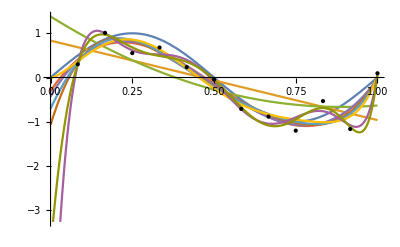

```mathematica
Plot[{Sin[2π x],%},{x,0,1},Epilog->{Point/@data}]
```